```mathematica
Clear[Lx,Ly,A,
sx2d,SX2D,sx2dp,SX2DP,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,cx2dp,CX2DP,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
Lx=32;
Ly=32;
A=Lx*Ly;
```

```mathematica
B=1/Ly;
```

```mathematica
(*--- We choose gauge A = (-By,0,0) ---*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2 Exp[I B k],sx2d[j+1+k Lx,j+k Lx]=I/2 Exp[-I B k]},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx2dp[i_Integer,j_Integer]=0;

Do[{sx2dp[(k+1)Lx,1+k Lx]=-I/2 Exp[I B k],sx2dp[1+k Lx,(k+1)Lx]=I/2 Exp[-I B k]},{k,0,Ly-1}]

SX2DP=Table[sx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2 Exp[I B k],cx2d[j+1+k Lx,j+k Lx]=1/2 Exp[-I B k]},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx2dp[i_Integer,j_Integer]=0;

Do[{cx2dp[(1+k)Lx,1+k Lx]=1/2 Exp[I B k],cx2dp[1+k Lx,(1+k)Lx]=1/2 Exp[-I B k]},{k,0,Ly-1}]

CX2DP=Table[cx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianWSM1, HamiltonianWSM2]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
(* HamiltonianQAHI[t_,t0_,m_,α_]:=t*(KroneckerProduct[SX2D+α*SX2DP,σ1]+KroneckerProduct[SY2D+α*SY2DP, σ2])+KroneckerProduct[-m*Cons+t0*(CX2D+CY2D+α*CX2DP+α*CY2DP),σ3] *)
```

```mathematica
(* HamiltonianQAHI[t_,t0_,m_,kz_]:=t*(KroneckerProduct[SX2D,σ1]+KroneckerProduct[SY2D, σ2])+KroneckerProduct[-m*Cons+t0*(CX2D+CY2D),σ3] +Cos[kz]*KroneckerProduct[Cons,σ3] *)
```

```mathematica
HamiltonianWSM1[t_,t0_,m_,tz_,kz_,αx_, αy_]:=t*(KroneckerProduct[SX2D+αx*SX2DP,σ1]+KroneckerProduct[SY2D+αy*SY2DP, σ2])+KroneckerProduct[2*Cons-t0*(CX2D+CY2D+αx*CX2DP+αy*CY2DP),σ3]+KroneckerProduct[(tz *Cos[kz]-m)*Cons,σ3]
```

```mathematica
HamiltonianWSM2[t_,m_,kz_,αx_, αy_,tz_]:=2t*(KroneckerProduct[SX2D+αx*SX2DP,σ1]+KroneckerProduct[SY2D+αy*SY2DP, σ2])+2m * KroneckerProduct[2*Cons-(CX2D+CY2D+αx*CX2DP+αy*CY2DP),σ3]+KroneckerProduct[(2 t *Cos[kz])*Cons,σ3]-2 tz * KroneckerProduct[SX2D+αx*SX2DP,σ0]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange,β]
```

```mathematica
β=-1.75;
```

```mathematica
{val,vec}=Eigensystem[HamiltonianWSM1[1.,1.,0,1,(β π)/2,0,0]];
```

```mathematica
ValVecAHI=SortBy[Transpose[{val,vec}],First];
```

```mathematica
ValAHI=Table[{j,Re[ValVecAHI[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange=Table[ValAHI[[j,2]],{j,1,2 A}];
```

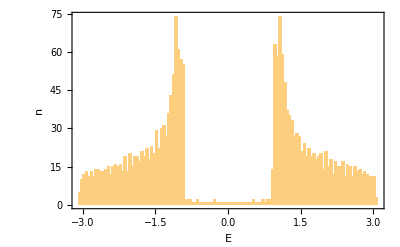

```mathematica
Show[Histogram[val,100],PlotRange-> All, Frame-> True, FrameLabel-> {"E","n"},BaseStyle-> 16,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}}]
```

```mathematica
(*zeroMagfield*)
```

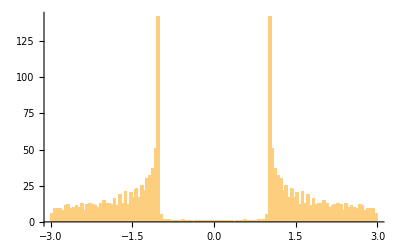

-Graphics-

```mathematica
(** B = 1 **)
```

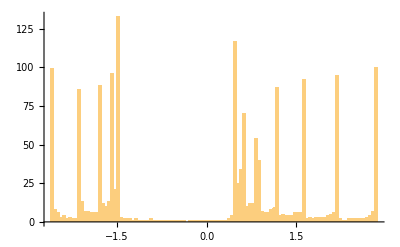

-Graphics-

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val2,vec2,ValVecAHI2,ValAHI2,ValAHIRange2,β];
β=2;
```

```mathematica
{val2,vec2}=Eigensystem[HamiltonianWSM2[1.,3.,(β π)/2,0,0,0]];
```

```mathematica
ValVecAHI2=SortBy[Transpose[{val2,vec2}],First];
```

```mathematica
ValAHI2=Table[{j,Re[ValVecAHI2[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange2=Table[ValAHI2[[j,2]],{j,1,2 A}];
```

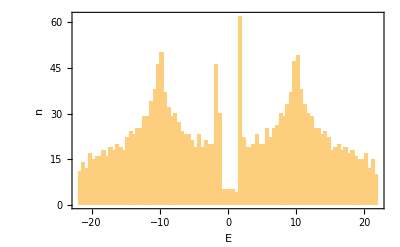

```mathematica
Show[Histogram[val2,100],PlotRange->All, Frame-> True, FrameLabel-> {"E","n"},BaseStyle-> 16,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}}]
```

```mathematica
Clear[kzVector]
```

```mathematica
kzVector = N@Subdivide[-π,π,50]
```

{-3.14159,-3.01593,-2.89027,-2.7646,-2.63894,-2.51327,-2.38761,-2.26195,-2.13628,-2.01062,-1.88496,-1.75929,-1.63363,-1.50796,-1.3823,-1.25664,-1.13097,-1.00531,-0.879646,-0.753982,-0.628319,-0.502655,-0.376991,-0.251327,-0.125664,0.,0.125664,0.251327,0.376991,0.502655,0.628319,0.753982,0.879646,1.00531,1.13097,1.25664,1.3823,1.50796,1.63363,1.75929,1.88496,2.01062,2.13628,2.26195,2.38761,2.51327,2.63894,2.7646,2.89027,3.01593,3.14159}

```mathematica
NumPoints=Dimensions[kzVector][[1]]
```

51

```mathematica
(** 
Clear[b];
b={};
Do[{Clear[a],
a=Eigenvalues[HamiltonianWSM1[1.,1.,0,1,kzVector[[i]],1,1]],
Do[b=Append[b,{kzVector[[i]],a[[j]]}],{j,1,2*A}]},{i,1,NumPoints}]  **)
```

```mathematica
(** listplotOfenergyWithKz=Show[ListPlot[b,PlotRange-> { {-3.14,3.14} ,{-1,1}}],AxesLabel-> {"kz","Energy"},Frame-> True] **)
```

```mathematica
(** Show[ListPlot[b,PlotRange->{{-3.14,3.14},{-1,1}}],AxesLabel->{"kz","Energy"},Frame->True] **)
```

```mathematica
(*Older plots - with -2t_0 SX periodic in x **)
```

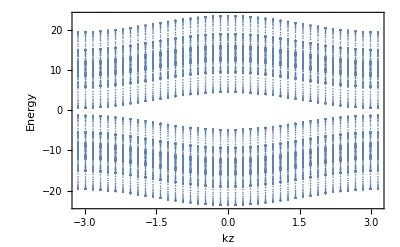

-Graphics-

-Graphics-

```mathematica
(** tz=0 **)
```

```mathematica
(** Clear[bb];
bb={};
Do[{Clear[a],
a=Eigenvalues[HamiltonianWSM2[1.,3.,kzVector[[i]],1,1,0]],
Do[bb=Append[bb,{kzVector[[i]],a[[j]]}],{j,1,2*A}]},{i,1,NumPoints}] **)
```

```mathematica
(** Show[ListPlot[bb,PlotRange-> { {-2.5,-1} ,{-0.5,0.5}},PlotStyle->PointSize[0.05]],AxesLabel-> {"kz","Energy"},Frame-> True] **)
```

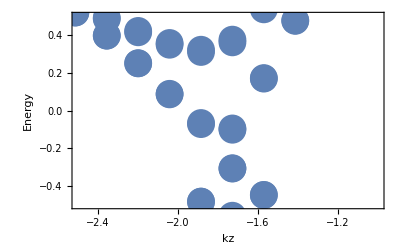

-Graphics-

```mathematica
(** Show[ListPlot[bb,PlotRange-> { {-3.14,3.14} ,{-2,2}},PlotStyle->PointSize[0.02]],AxesLabel-> {"kz","Energy"},Frame-> True] **)
```

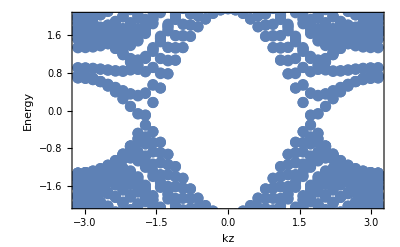

-Graphics-

```mathematica
(*Older plots - with -2t_0 SX periodic in y **)
```

-Graphics-

-Graphics-

```mathematica
(** tz=0.5 **)
```

```mathematica
(** Clear[bbb];
bbb={};
Do[{Clear[a],
a=Eigenvalues[HamiltonianWSM2[1.,3.,kzVector[[i]],1,1,0.5]],
Do[bbb=Append[bbb,{kzVector[[i]],a[[j]]}],{j,1,2*A}]},{i,1,NumPoints}] **)
```

```mathematica
(** Show[ListPlot[bbb,PlotRange-> { {-2.5,-1} ,{-0.5,0.5}},PlotStyle->PointSize[0.05]],AxesLabel-> {"kz","Energy"},Frame-> True] **)
```

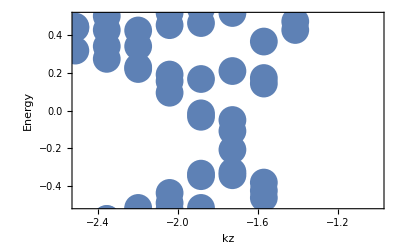

-Graphics-

```mathematica
(** Show[ListPlot[bbb,PlotRange-> { {-3.14,3.14} ,{-2,2}},PlotStyle->PointSize[0.02]],AxesLabel-> {"kz","Energy"},Frame-> True] **)
```

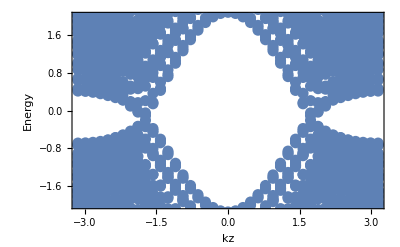

-Graphics-

```mathematica
(** tz=1 **)
```

```mathematica
(** Clear[bbbb];
bbbb={};
Do[{Clear[a],
a=Eigenvalues[HamiltonianWSM2[1.,3.,kzVector[[i]],1,1,1]],
Do[bbbb=Append[bbbb,{kzVector[[i]],a[[j]]}],{j,1,2*A}]},{i,1,NumPoints}] **)
```

```mathematica
(** Show[ListPlot[bbbb,PlotRange-> { {-2.5,-1} ,{-0.5,0.5}},PlotStyle->PointSize[0.05]],AxesLabel-> {"kz","Energy"},Frame-> True] **)
```

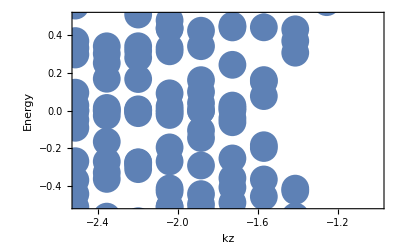

-Graphics-

```mathematica
(** Show[ListPlot[bbbb,PlotRange-> { {-3.14,3.14} ,{-2,2}},PlotStyle->PointSize[0.02]],AxesLabel-> {"kz","Energy"},Frame-> True] **)
```

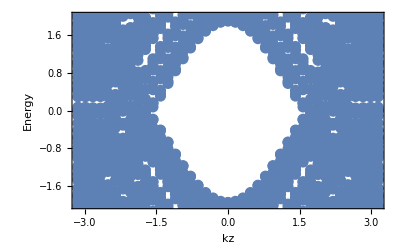

-Graphics-

```mathematica
(** tz=1.5 **)
```

```mathematica
(** Clear[bbbbb];
bbbbb={};
Do[{Clear[a],
a=Eigenvalues[HamiltonianWSM2[1.,3.,kzVector[[i]],1,1,1.5]],
Do[bbbbb=Append[bbbbb,{kzVector[[i]],a[[j]]}],{j,1,2*A}]},{i,1,NumPoints}] **)
```

```mathematica
(** Show[ListPlot[bbbbb,PlotRange-> { {-2.5,-1} ,{-0.5,0.5}},PlotStyle->PointSize[0.05]],AxesLabel-> {"kz","Energy"},Frame-> True] **)
```

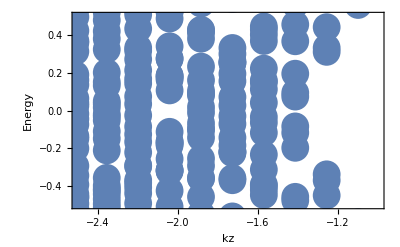

-Graphics-

```mathematica
(** Show[ListPlot[bbbbb,PlotRange-> { {-3.14,3.14} ,{-2,2}},PlotStyle->PointSize[0.02]],AxesLabel-> {"kz","Energy"},Frame-> True] **)
```

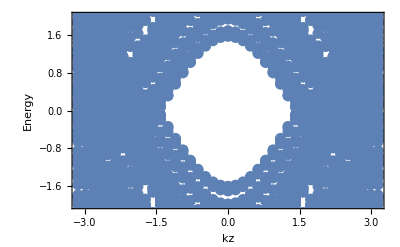

-Graphics-

```mathematica
(*--------------------quasicrystal--------------------------*)
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

2048

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
LineUp[x_]:=((1+√5)/2)^-1*(x-1)+14
LineDn[x_]:=((1+√5)/2)^-1*(x-2)-4
```

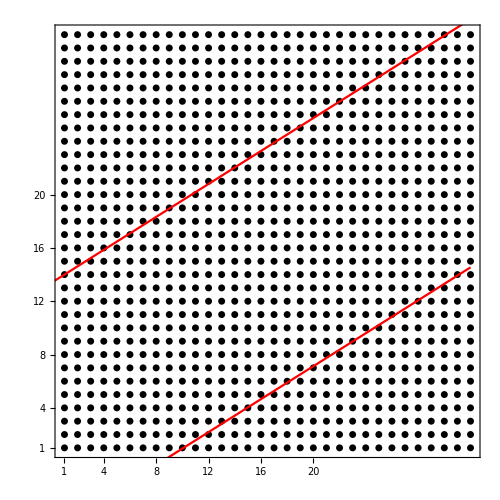

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
(*Plot[2/3*(x-1)+4,{x,0,Lx},PlotStyle-> Blue],Plot[2/3*(x-2)+3,{x,0,Lx},PlotStyle-> Blue],*)
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None}},
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList, XListKron, YListKron, Ux, Vy]
```

```mathematica
(**-----We want to count points inside the area of interest, store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Lx],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
FibonupNew;
```

```mathematica
Fibonlist=Sort[FibonupNew]
```

{1,2,3,4,5,6,7,8,9,10,33,34,35,36,37,38,39,40,41,42,43,65,66,67,68,69,70,71,72,73,74,75,76,77,97,98,99,100,101,102,103,104,105,106,107,108,109,110,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,787,788,789,790,791,792,793,794,795,796,797,798,799,800,821,822,823,824,825,826,827,828,829,830,831,832,855,856,857,858,859,860,861,862,863,864,888,889,890,891,892,893,894,895,896,922,923,924,925,926,927,928,955,956,957,958,959,960,989,990,991,992,1023,1024}

```mathematica
(** Fibonup2={}; **)
```

```mathematica
(** Do[Do[Fibonup2=Append[Fibonup2,x+(y-1)*Lx],{y,6,15}],{x,6,15}]**)
```

```mathematica
(** Fibonup2**)
```

```mathematica
(** Clear[Fibonup]**)
```

```mathematica
(** Fibonup = Fibonup2**)
```

```mathematica
YList = Ceiling[Fibonlist/Lx];
```

```mathematica
XList = Fibonlist - (YList - 1)Lx;
```

```mathematica
(**Check that the list is correct**)
```

```mathematica
XList + (YList-1)*Lx - Fibonlist
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];
```

```mathematica
YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];
```

```mathematica
Ux =DiagonalMatrix[ Exp[2 π I XListKron /Lx]];
```

```mathematica
Vy = DiagonalMatrix[Exp[2 π I YListKron/Ly]];
```

```mathematica
(**--Compare with the previous (manually calculated) Fibonup for 20x20 sites--**)
```

```mathematica
(**--Fibonup={1,22,23,43,44,45,65,66,86,87,88,108,109,110,130,131,151,152,153,173,174,194,195,196,216,217,218,238,239,259,260};--**)
```

```mathematica
(**----Group the orbitals in the sites in Fibonlist ---**)
```

```mathematica
Fibonup = 2 * Fibonlist -1;
```

```mathematica
Fibondown = 2 * Fibonlist;
```

```mathematica
(**-- Fibondown=Table[Fibonlist[[j]]+A,{j,1,Dimensions[Fibonlist][[1]]}]; --**)
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
TotalFibon = Sort[TotalFibon]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,1009,1010,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023,1024,1035,1036,1037,1038,1039,1040,1041,1042,1043,1044,1045,1046,1047,1048,1049,1050,1051,1052,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1069,1070,1071,1072,1073,1074,1075,1076,1077,1078,1079,1080,1081,1082,1083,1084,1085,1086,1087,1088,1103,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118,1119,1120,1121,1122,1123,1124,1125,1126,1127,1128,1129,1130,1131,1132,1133,1134,1135,1136,1137,1138,1139,1140,1141,1142,1143,1144,1145,1146,1147,1148,1149,1150,1151,1152,1171,1172,1173,1174,1175,1176,1177,1178,1179,1180,1181,1182,1183,1184,1185,1186,1187,1188,1189,1190,1191,1192,1193,1194,1195,1196,1197,1198,1199,1200,1201,1202,1203,1204,1205,1206,1207,1208,1209,1210,1211,1212,1213,1214,1215,1216,1237,1238,1239,1240,1241,1242,1243,1244,1245,1246,1247,1248,1249,1250,1251,1252,1253,1254,1255,1256,1257,1258,1259,1260,1261,1262,1263,1264,1265,1266,1267,1268,1269,1270,1271,1272,1273,1274,1275,1276,1277,1278,1279,1280,1305,1306,1307,1308,1309,1310,1311,1312,1313,1314,1315,1316,1317,1318,1319,1320,1321,1322,1323,1324,1325,1326,1327,1328,1329,1330,1331,1332,1333,1334,1335,1336,1337,1338,1339,1340,1341,1342,1343,1344,1371,1372,1373,1374,1375,1376,1377,1378,1379,1380,1381,1382,1383,1384,1385,1386,1387,1388,1389,1390,1391,1392,1393,1394,1395,1396,1397,1398,1399,1400,1401,1402,1403,1404,1405,1406,1407,1408,1439,1440,1441,1442,1443,1444,1445,1446,1447,1448,1449,1450,1451,1452,1453,1454,1455,1456,1457,1458,1459,1460,1461,1462,1463,1464,1465,1466,1467,1468,1469,1470,1471,1472,1507,1508,1509,1510,1511,1512,1513,1514,1515,1516,1517,1518,1519,1520,1521,1522,1523,1524,1525,1526,1527,1528,1529,1530,1531,1532,1533,1534,1535,1536,1573,1574,1575,1576,1577,1578,1579,1580,1581,1582,1583,1584,1585,1586,1587,1588,1589,1590,1591,1592,1593,1594,1595,1596,1597,1598,1599,1600,1641,1642,1643,1644,1645,1646,1647,1648,1649,1650,1651,1652,1653,1654,1655,1656,1657,1658,1659,1660,1661,1662,1663,1664,1709,1710,1711,1712,1713,1714,1715,1716,1717,1718,1719,1720,1721,1722,1723,1724,1725,1726,1727,1728,1775,1776,1777,1778,1779,1780,1781,1782,1783,1784,1785,1786,1787,1788,1789,1790,1791,1792,1843,1844,1845,1846,1847,1848,1849,1850,1851,1852,1853,1854,1855,1856,1909,1910,1911,1912,1913,1914,1915,1916,1917,1918,1919,1920,1977,1978,1979,1980,1981,1982,1983,1984,2045,2046,2047,2048}

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]]
```

1142

```mathematica
NOrbitalsQuasi/2
```

571

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsQuasi
```

906

```mathematica
PercentageDataIn = N[NOrbitalsQuasi/(2*A)]
```

0.557617

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
Dimensions[F1]
```

{2048}

```mathematica
(**-- a=F1;
Do[
a=Drop[a,{TotalFibon[[NOrbitalsQuasi-i]]}],
{i,0,NOrbitalsQuasi-1,1}
] --**)
```

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
(**-------------------------------**)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[TabRenorEnergies]
```

```mathematica
TabRenorEnergies={}
```

{}

```mathematica
Do[{Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D],
HTrial=HamiltonianWSM2[1.,3.,kzVector[[p]],1,0,0],
(*---------------------------------------------------------*)
Hfbfb[i_Integer,j_Integer]=0,
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsQuasi}
],
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}],
(*---------------------------------------------------------*)
H2d2d[i_Integer,j_Integer]=0,
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
],
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}],
(*------------------------------------------------------*)
H2dfb[i_Integer,j_Integer]=0,

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsQuasi}
],
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsQuasi}],
(*-------------------------------------------------*)
Hfb2d[i_Integer,j_Integer]=0,

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsOutside}
],
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsOutside}],

(*---------------------------------------------------------------------------------------------------------------------------------*)
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon],
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D].H2DFB),
(**------Check that HFibonRenor is Hermitian------**)
OnlyEigenvalue=Eigenvalues[HFibonRenor],
percentageOfOrbitalsInside = N[NOrbitalsQuasi/(2*A)],
NSitesInside = NOrbitalsQuasi/2,
Do[TabRenorEnergies = Append[TabRenorEnergies,{kzVector[[p]],OnlyEigenvalue[[i]]}],{i,1,NOrbitalsQuasi}]
},{p,1,NumPoints}]
```

```mathematica
TabRenorEnergies=Sort[Re[TabRenorEnergies]];
```

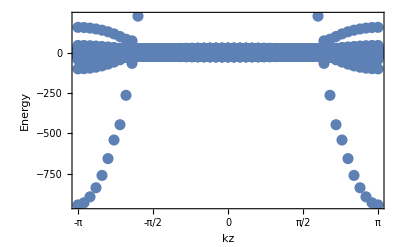

```mathematica
Show[ListPlot[Re[TabRenorEnergies],PlotRange-> All,PlotStyle->PointSize[0.02]],FrameTicks-> {{-π,-π/2,0,π/2,π},Automatic,{},{}},BaseStyle-> 18,AxesLabel-> {"kz","Energy"},Frame-> True]
```

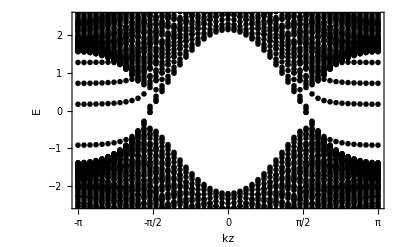

```mathematica
A=Show[ListPlot[Re[TabRenorEnergies],PlotRange-> { {-π,π} ,{-2.5,2.5}},PlotStyle->{PointSize[0.01],Black}],FrameTicks-> {{-π,-π/2,0,π/2,π},Automatic,{},{}},BaseStyle-> 18,FrameLabel-> {"kz","E"},Frame-> True]
```

```mathematica
(** Export["FibonEnergies32x32-linUp+14linDn-4Magnetic1byLy-xPeriod-yOpenPRLModel.dat",TabRenorEnergies] **)
```

FibonEnergies32x32-linUp+14linDn-4Magnetic1byLy-xPeriod-yOpenPRLModel.dat

```mathematica
Dimensions[TabRenorEnergies]
```

{58242,2}

```mathematica
Dimensions[kzVector][[1]]*NOrbitalsQuasi
```

58242

```mathematica
TabRenorEnergies[[NOrbitalsQuasi/2 +1]]
```

{-3.14159,-10.0737}

```mathematica
{LandauLevelEnergies1 = {},Do[LandauLevelEnergies1 = Append[LandauLevelEnergies1, TabRenorEnergies[[NOrbitalsQuasi/2+1+k*NOrbitalsQuasi]]],{k,0,Dimensions[kzVector][[1]]-1}]};
```

```mathematica
{LandauLevelEnergies2 = {},Do[LandauLevelEnergies2 = Append[LandauLevelEnergies2, TabRenorEnergies[[NOrbitalsQuasi/2+3+k*NOrbitalsQuasi]]],{k,0,Dimensions[kzVector][[1]]-1}]};
```

```mathematica
LandauLevelEnergies
```

{{-3.14159,-1.38489},{-3.01593,-1.37862},{-2.89027,-1.35981},{-2.7646,-1.32849},{-2.63894,-1.28332},{-2.51327,-1.2224},{-2.38761,-1.14555},{-2.26195,-1.04678},{-2.13628,-0.921161},{-2.01062,-0.758449},{-1.88496,-0.576041},{-1.75929,-0.477733},{-1.63363,-0.0514701},{-1.50796,0.24332},{-1.3823,0.50392},{-1.25664,0.752668},{-1.13097,0.989161},{-1.00531,1.21104},{-0.879646,1.41539},{-0.753982,1.59927},{-0.628319,1.75992},{-0.502655,1.8949},{-0.376991,2.00212},{-0.251327,2.07992},{-0.125664,2.12709},{0.,2.1429},{0.125664,2.12709},{0.251327,2.07992},{0.376991,2.00212},{0.502655,1.8949},{0.628319,1.75992},{0.753982,1.59927},{0.879646,1.41539},{1.00531,1.21104},{1.13097,0.989161},{1.25664,0.752668},{1.3823,0.50392},{1.50796,0.24332},{1.63363,-0.0514701},{1.75929,-0.477733},{1.88496,-0.576041},{2.01062,-0.758449},{2.13628,-0.921161},{2.26195,-1.04678},{2.38761,-1.14555},{2.51327,-1.2224},{2.63894,-1.28332},{2.7646,-1.32849},{2.89027,-1.35981},{3.01593,-1.37862},{3.14159,-1.38489}}

```mathematica
(** Export["LandauLevelFibonEnergies32x32-linUp+14linDn-4Magnetic1byLy-xPeriod-yOpenPRLModel.dat",LandauLevelEnergies]; **)
```

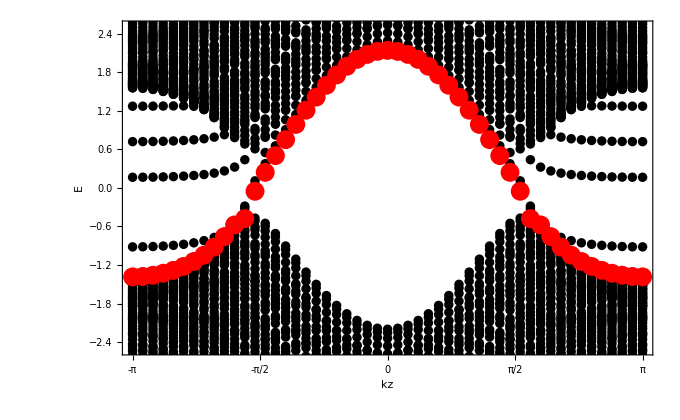

```mathematica
Show[A,ListPlot[Re[LandauLevelEnergies1],PlotStyle->{Red,PointSize[0.02]},PlotRange->{{-π/2,π/2},All}],FrameStyle-> {Black,Black,Black,Black}]
```

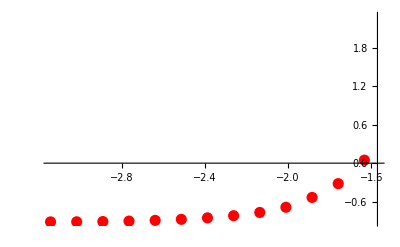

```mathematica
A1=ListPlot[Re[LandauLevelEnergies2],PlotStyle->{Red,PointSize[0.02]},PlotRange->{{-π,-π/2},All}]
```

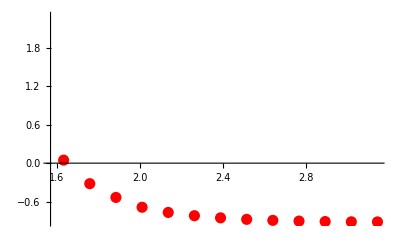

```mathematica
A2=ListPlot[Re[LandauLevelEnergies2],PlotStyle->{Red,PointSize[0.02]},PlotRange->{{π/2,π},All}]
```

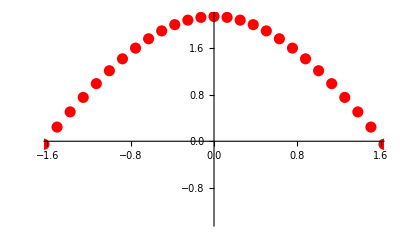

```mathematica
A3=ListPlot[Re[LandauLevelEnergies1],PlotStyle->{Red,PointSize[0.02]},PlotRange->{{-π/2,π/2},All}]
```

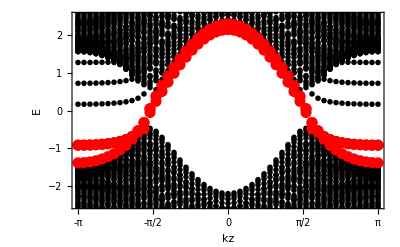

```mathematica
Show[A,A1,A2,A3]
```

```mathematica
(** LineUp[x_]:=((1+√5)/2)^-1*(x-1)+4
LineDn[x_]:=((1+√5)/2)^-1*(x-2)-2 for 28x28 **)
```

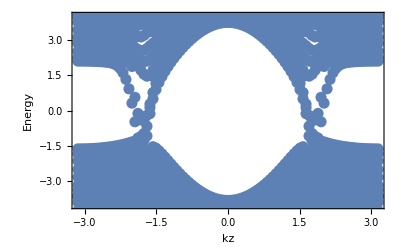

-Graphics-

```mathematica
(** TabRenorEnergiesPlus4Minus2 **)
```

```mathematica
TabRenorEnergiesPlus4Minus2
```

TabRenorEnergiesPlus4Minus2

```mathematica
(** LineUp[x_]:=((1+√5)/2)^-1*(x-1)+4
LineDn[x_]:=((1+√5)/2)^-1*(x-2)-2 for 20x20 **)
```

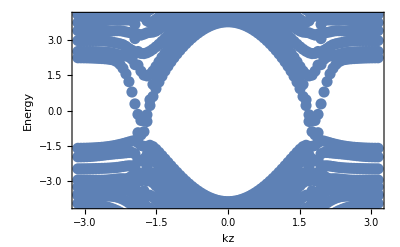

-Graphics-

```mathematica
(** TabRenorEnergiesPlus14Minus4 **)
```

```mathematica
(** LineUp[x_]:=((1+√5)/2)^-1*(x-1)+14
LineDn[x_]:=((1+√5)/2)^-1*(x-2)-4 for 20x20 **)
```

-Graphics-

```mathematica
(** LineUp[x_]:=((1+√5)/2)^-1*(x-1)+4
LineDn[x_]:=((1+√5)/2)^-1*(x-2)+2 **)
```

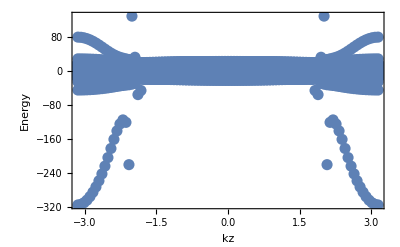

-Graphics-